If[x≥0,x,0]

0

0

-0.13544+1.5955 If[-0.925348-0.0826388 x1-3.4047 x2≥0,-0.925348-0.0826388 x1-3.4047 x2,0]-1.77132 If[-0.692523-0.581202 x1-2.28887 x2≥0,-0.692523-0.581202 x1-2.28887 x2,0]+0.966507 If[-0.214693+0.157842 x1-2.23643 x2≥0,-0.214693+0.157842 x1-2.23643 x2,0]+1.07158 If[0.434719-0.898793 x1-1.36831 x2≥0,0.434719-0.898793 x1-1.36831 x2,0]+0.58872 If[0.528533+1.23785 x1-1.2961 x2≥0,0.528533+1.23785 x1-1.2961 x2,0]+0.0511649 If[0.257869-0.0304579 x1-1.2508 x2≥0,0.257869-0.0304579 x1-1.2508 x2,0]-0.634538 If[-1.21653+0.888938 x1-0.911438 x2≥0,-1.21653+0.888938 x1-0.911438 x2,0]-0.306917 If[-0.0798752-0.807267 x1-0.312903 x2≥0,-0.0798752-0.807267 x1-0.312903 x2,0]-0.0817428 If[-0.931704+0.191615 x1-0.075847 x2≥0,-0.931704+0.191615 x1-0.075847 x2,0]+1.68639 If[-2.1723+0.00309064 x1-0.0160883 x2≥0,-2.1723+0.00309064 x1-0.0160883 x2,0]+0.255586 If[0.291798+0.00495489 x1+0.130951 x2≥0,0.291798+0.00495489 x1+0.130951 x2,0]+0.147045 If[-0.304519-0.115965 x1+0.160339 x2≥0,-0.304519-0.115965 x1+0.160339 x2,0]-0.82026 If[-1.84685-0.412837 x1+0.186893 x2≥0,-1.84685-0.412837 x1+0.186893 x2,0]-0.207016 If[-0.0269045-0.249996 x1+0.20998 x2≥0,-0.0269045-0.249996 x1+0.20998 x2,0]+0.332869 If[0.674581-0.391735 x1+0.476703 x2≥0,0.674581-0.391735 x1+0.476703 x2,0]+0.468234 If[-0.801151-2.47346 x1+2.31823 x2≥0,-0.801151-2.47346 x1+2.31823 x2,0]

0.0304027

0.0304027

0.0497883-0.00259129 If[0.483765-0.0862997 x1-0.776693 x2≥0,0.483765-0.0862997 x1-0.776693 x2,0]+0.00379095 If[0.995011-0.569652 x1-0.718505 x2≥0,0.995011-0.569652 x1-0.718505 x2,0]-0.00109702 If[-0.18874+0.0725762 x1-0.540959 x2≥0,-0.18874+0.0725762 x1-0.540959 x2,0]-0.000876537 If[0.778719-0.527343 x1-0.447011 x2≥0,0.778719-0.527343 x1-0.447011 x2,0]+0.633274 If[-1.30647+0.110959 x1-0.407081 x2≥0,-1.30647+0.110959 x1-0.407081 x2,0]-0.00716508 If[0.530957-0.236064 x1-0.330779 x2≥0,0.530957-0.236064 x1-0.330779 x2,0]-0.00308162 If[0.209503-0.0550049 x1-0.227546 x2≥0,0.209503-0.0550049 x1-0.227546 x2,0]+0.634306 If[-0.49687-1.0564 x1+0.0488326 x2≥0,-0.49687-1.0564 x1+0.0488326 x2,0]

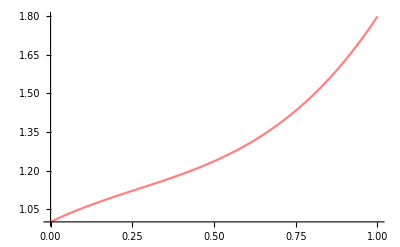

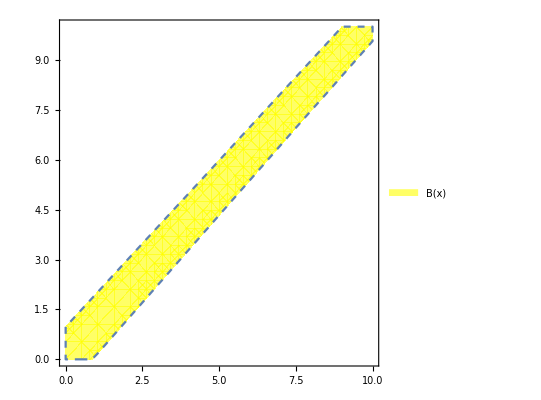

print[g_b]

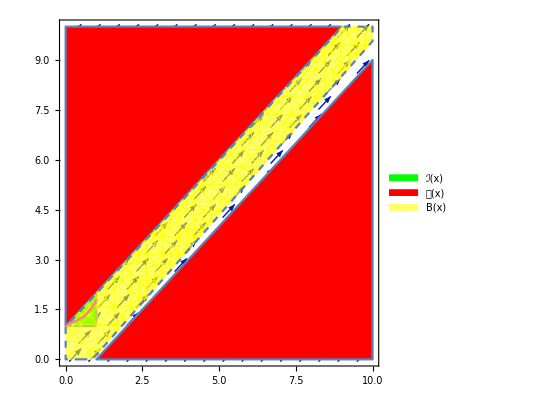

-Graphics-

```mathematica
(*phi=RegionPlot[(x≥0&&x≤0.7&&y≥0.7&&y≤1.5&&y-x<=0.8),{x,0,0.7},{y,0.7,1.5},PlotPoints->50,BoundaryStyle->Directive[RGBColor[0,0.5,0], Thin],PlotStyle->Directive[Blue]]
(*phi ->initial region *)
psi1=RegionPlot[(x≥0&&x≤8&&y≥0&&y≤8&&(y-x)*(y-x)>=1),{x,0,8},{y,0,8},PlotPoints->70,PlotStyle->Directive[Red],BoundaryStyle->Directive[RGBColor[0.5,0,0], Opacity[0.05],Thin]]*)
(* we first give ReLU fuction*)
relu[x_] =If[x>=0,x,0]
(*psi -> unsafe region*)

(*B(x,xˆ)=0.9227x1*x1+0.2348v1*v1+0.9227x2*x2+0.2348v2*v2+0.006x1*v1−0.006x2*v1−0.006x1*v2−0.006x2*v2−0.4696v1*v2−1.845x1x2−0.0002*x2+0.0728,*)
(* this B is only for test*)

x3 =0
x4 =0

(*bc = -1.95893932849805*relu[-3.06745666070064*x1-2.18565116340357*x2+0.492202911674726*x3-0.601142863229924*x4-1.49399989357892]+0.042807425485326*relu[-1.90299025788477*x1+1.27130766808303*x2+0.202256308830197*x3-1.05681283173161*x4+0.891207095284904]+0.541096974932025*relu[-1.44067942289039*x1+1.46196271099073*x2-0.393688922194866*x3-1.20971718593056*x4-0.458568122422984]+1.80501140477239*relu[-0.823095249061938*x1-0.445549217854596*x2+0.45489530862806*x3+1.74772062192633*x4-0.150143782377428]+0.283266528000333*relu[-0.699634490326854*x1+0.607013674453812*x2-0.290454273928679*x3-0.436341785923251*x4+0.293946192144029]-1.03978901444535*relu[-0.432038608228579*x1+0.350457859210165*x2-0.0524785990807935*x3+1.03438561487001*x4-0.427984255879527]+0.517845683025612*relu[-0.317368302367596*x1+0.417297866981916*x2-1.45021581230588*x3-1.70869806051072*x4+0.933481285090467]-0.129262950229095*relu[0.0375460344475947*x1+0.00517751452902003*x2+1.15104476959909*x3-1.1316646746778*x4-0.527441870451535]+0.230244579222581*relu[0.0762006815474609*x1-0.368857681409751*x2-0.0554039065781252*x3-1.10895336657976*x4-0.67577790453123]-0.377731089590759*relu[0.139087837022083*x1-0.121032617853381*x2+1.97642725030985*x3+1.35093449654761*x4+0.0378997958036385]+1.52112278407188*relu[0.181137540223159*x1-1.56599681334452*x2-0.0359066776805434*x3+0.189529011031616*x4-0.766865619315998]-0.111795916949035*relu[0.181792127853433*x1+0.0358262340863845*x2+1.57579118124003*x3+0.541583637828533*x4-0.657901800544883]-0.743040996728229*relu[0.722203435765187*x1-0.837608658918819*x2+2.8071489815537*x3-1.04661600222788*x4-0.853250592776218]-0.10909431646357*relu[1.05028347056777*x1-0.92688728488997*x2-0.469071688451793*x3+0.257696156297519*x4+0.203032269378149]+0.366699582579535*relu[1.20550898212378*x1-1.29214237273389*x2-0.78683771064422*x3-1.29438574225777*x4+0.904878547717075]+0.587574004567898*relu[2.3339347879447*x1-2.30637307923457*x2-1.02424831242276*x3+0.0230045269014443*x4-1.04190975660202]-0.188212177976341*)
(*bc = -0.884244542265045*relu[-1.5454342408626*x+0.389421867613319*y+0.641497719701889*x3-1.49957454665973*x4-0.788831132658342]+0.495812842726736*relu[-1.20573320037251*x+1.17241574673601*y-0.34549759247628*x3+0.768077007828974*x4-0.259030106813608]+0.400948545893493*relu[-0.788396560827678*x+0.77197485292358*y+1.37035260042867*x3+0.388518122533327*x4-0.580768778552474]+0.184303850863669*relu[-0.782861127770446*x+0.749551110316921*y+0.767471034732239*x3-0.0305187353304383*x4+0.368679331415413]+0.580964479361525*relu[-0.778977624305882*x+0.198534254099716*y+0.523644702233966*x3+0.153620995863471*x4-0.673901213209626]-1.28499827038157*relu[-0.659095936077543*x+0.040168096851337*y-0.970225509692925*x3+0.268224221921974*x4-0.26540021642565]-0.232152278683067*relu[-0.593970106116713*x+0.644901224874934*y-0.786889719313109*x3-0.77257297593204*x4+0.421063439450774]-0.717151396235161*relu[-0.501717950532894*x-0.510389557343015*y-0.0691788543777268*x3-0.613053346681068*x4+0.526771642663559]-0.00173192750996577*relu[-0.441110496781229*x-0.430497131143339*y-0.900032664233997*x3+0.378242574586411*x4-0.816195830000279]-0.41205819477833*relu[-0.397969902248279*x-0.155882037799488*y+0.50490309916375*x3-0.446644348349988*x4-0.268569588277714]-0.651593498904306*relu[-0.183907933765682*x-0.497034937607809*y+1.00958938098255*x3-0.550139805303046*x4-0.123032705368391]+0.124097368232535*relu[-0.170981174189519*x-1.70473748006411*y-0.656898992181073*x3-1.38027287379307*x4-0.84930550134649]-0.343670665326598*relu[-0.0518405025205465*x+0.0314029348767455*y-0.895365542225653*x3-1.51990343971836*x4+0.664036603650592]-0.830861759712741*relu[-0.0416457648530211*x+0.00400962282822978*y+0.0817762842596415*x3+0.477787756041*x4-0.0851858122290517]+0.497081213149162*relu[-0.00134184266584635*x+0.0420188627717125*y-0.813376978789925*x3+2.4019282667092*x4+0.587536633618811]+0.298609858303979*relu[1.02992810971779*x-1.11071340943805*y-0.632144084994595*x3+0.192866154013205*x4+0.37783598469218]+0.545124122969228*)
(*bc=0.9227*x1*x1 + 0.9227*x2*x2 -1.845*x1*x2  - 0.0002*x2 + 0.0728*)
bc = 0.468233667489537*relu[-2.47345653158861*x1+2.31822817049393*x2-0.295640064973835*x3-1.91512398241388*x4-0.801150621802473]+1.07157971918809*relu[-0.898792754682817*x1-1.36831358542676*x2-1.37734155593681*x3+0.174681023661614*x4+0.434719074534784]-0.306916761697179*relu[-0.807266924414832*x1-0.312902674705674*x2+1.43801189386199*x3+0.977097471410741*x4-0.0798751683942861]-1.77132239251502*relu[-0.581202398306555*x1-2.28887485001046*x2-0.50002619880897*x3+0.674272818879106*x4-0.692523475793253]-0.820260086910851*relu[-0.412836674806562*x1+0.186892850161291*x2-0.199000691629567*x3-0.883346262806037*x4-1.8468459516147]+0.33286892115579*relu[-0.391735211656048*x1+0.476702684147217*x2-1.1534020394472*x3-2.52343395944264*x4+0.674581377539614]-0.207016114803931*relu[-0.249996463351338*x1+0.209979786590457*x2+2.00082905557458*x3+0.810260239485106*x4-0.0269045103232186]+0.14704489826871*relu[-0.115965490288639*x1+0.160339232236668*x2-0.3931541961787*x3-1.18190281372841*x4-0.304519142533639]+1.5955011779023*relu[-0.0826388202526234*x1-3.40470036049006*x2-1.66564306429149*x3+0.362702440856748*x4-0.925348128697858]+0.0511648786374518*relu[-0.0304579362370926*x1-1.25079902882795*x2-0.792641313039323*x3+1.05430244179764*x4+0.257869429957563]+1.68638728622742*relu[0.00309063976745693*x1-0.0160883082848729*x2-0.10433475095528*x3-1.1371636738034*x4-2.17230187504762]+0.2555858251854*relu[0.00495489317168438*x1+0.130950998440245*x2-1.94793526226148*x3-1.26286753717442*x4+0.291798476273517]+0.966507243271604*relu[0.157842092114713*x1-2.23642990967513*x2+0.742821188568443*x3-0.0331030230512255*x4-0.214692585571679]-0.0817427828968695*relu[0.191614672129839*x1-0.0758469747775256*x2+0.869466027078459*x3-1.29269828579892*x4-0.931703595378306]-0.634538186158738*relu[0.888937585386507*x1-0.91143832697544*x2+0.946693431221522*x3-0.0317483600484441*x4-1.21652537895425]+0.588719731121249*relu[1.23785317449275*x1-1.29610318770792*x2-0.0517773345622526*x3-0.302871675498303*x4+0.528533194530017]-0.135439662887632
(*uˆ(x,ˆx,u)=0.8x1−0.8x2+1.5ˆx1−1.5ˆx2+u.*)
(*this is controller*)

(* xuebai *)
initialPlot=RegionPlot[(x1≥0&&x1≤1&&x2≥1&&x2≤10&&x2-x1<=1),{x1,0,1},{x2,1,10},PlotStyle->Directive[Green],PlotLegends->SwatchLegend[{"ℐ(x)"}]];
(*initialPlot = Graphics[Line[{{0.1,0.75},{0.6,1.35}}]];*)
unsafePlot=RegionPlot[(x1≥0&&x1≤10&&x2≥0&&x2≤10&&(x2-x1)*(x2-x1)>=1),{x1,0,10},{x2,0,10},PlotStyle->Directive[Red],PlotLegends->SwatchLegend[{"𝒰(x)"}]];
bcPlot=RegionPlot[(x1≥0&&x1≤10&&x2≥0&&x2≤10&&bc<=1),{x1,0,10},{x2,0,10},BoundaryStyle->{Dashed},PlotStyle->Directive[Opacity[.6],Yellow],PlotLegends->SwatchLegend[{"B(x)"}]];
u = Random[Real,{-0.05,0.05}]
x5 = u
uhat = 0.63430554219462*relu[-1.05640475525405*x1+0.0488326204142155*x2-0.275281155118706*x3+0.216757832345094*x4-2.68037239214522*x5-0.415379758734497]+0.00379095151734818*relu[-0.569651615300073*x1-0.718505208048128*x2-0.190829555781395*x3-0.552923116347701*x4-1.71152456167048*x5+1.0470455751068]-0.000876536845683693*relu[-0.527342839175581*x1-0.447010877005243*x2+1.71686111752574*x3+0.956162485805343*x4-1.82511697864463*x5+0.83420715795233]-0.00716507906758264*relu[-0.236063750720613*x1-0.3307792904271*x2+0.421786924749281*x3-1.94704691186014*x4+1.47230024505477*x5+0.486194611307155]-0.00259129362019393*relu[-0.0862997443758153*x1-0.776692853060658*x2-2.1847414235014*x3-0.550363385811632*x4+0.465947349446945*x5+0.469599105252855]-0.00308161689954787*relu[-0.0550049305397898*x1-0.227546097768592*x2-0.182958181573198*x3+1.19635940050532*x4+1.62772039819868*x5+0.160015613690608]-0.00109701972867817*relu[0.072576171795998*x1-0.540959415339216*x2-0.975007443647644*x3-0.900611450651645*x4+0.685452796769246*x5-0.209579966371362]+0.633273818648491*relu[0.110958960034177*x1-0.407080831229605*x2+1.06633998496271*x3+0.765893528230141*x4+0.611740528104391*x5-1.32507225978689]+0.0497883377675418
(*uhat = 0.8*x1+1.5*x2+u*)

(*uhat = -1.99525335935363*relu[-1.45181591589465*x+0.0115699524133529*y+0.353279091334835*x3+0.216686394585325*x4-0.661786996447191*x5-0.189589665670093]-0.00262144849895737*relu[-1.28838774180751*x-0.33917968104393*y+0.274691264833212*x3+1.39773203541569*x4-0.780001774481891*x5+1.26597841272792]-0.15336707746233*relu[-1.25760868593536*x-1.79763719646576*y-0.130388575899045*x3+0.116163293723147*x4+0.0118270066467433*x5-2.20229303795275]+0.670842105852222*relu[-0.82566006126899*x-0.0490107066974787*y+0.284369211852316*x3-0.256782239128023*x4-1.60988170785305*x5-0.214673163370514]-0.923894941629845*relu[-0.468630912504019*x+0.0287009087381236*y+0.238317927711118*x3+1.25853336762075*x4-0.920719061916972*x5-0.946527401982451]-0.0137503236815635*relu[-0.0198158112234174*x+0.00152419485147087*y-0.759135765900395*x3+0.22625569714838*x4+1.74176392164001*x5+0.0803041972063283]+0.0258852880996615*relu[0.16417169511794*x+0.00298979066149963*y-1.70453987149348*x3+0.693718507252594*x4-2.08899126740029*x5-1.17410032827435]+0.00141646049014885*relu[0.170715971522104*x-1.15550227156574*y+0.123567903372231*x3-0.352526092387353*x4-1.02964182066095*x5-0.440152370366425]-0.0440324832305781*)
(*uhat = -1.78863251602674*relu[-1.15284513837517*x1-0.46921627620952*x2-0.387229466682093*x3+0.144694673034578*x4-0.549046894192871*x5+0.00255335722163473]-0.367777714413742*relu[-1.15104999047042*x1-1.09675476155998*x2+1.42221567981911*x3-0.206599689443102*x4-1.25805132784115*x5-0.0897303833650123]-0.00266333197556452*relu[-0.887043099299839*x1-0.0157554540093694*x2-0.642512367393646*x3-0.429830602483124*x4+0.395337173670947*x5+0.425377037707252]-0.397523245137382*relu[-0.469038268140349*x1+0.0245119347410819*x2-0.0892561527923562*x3-1.12862708823075*x4-0.387255371609413*x5-0.19081549023553]-1.48189702008959*relu[-0.206071892377149*x1-1.09130422658573*x2-0.866278419207306*x3+0.153907672110862*x4-1.29357357596357*x5-0.310436043086761]+0.000266989528356403*relu[-0.151715694476352*x1-0.185645010751303*x2+0.379998696472709*x3-0.853847226108817*x4-0.301139142882316*x5+0.576494268891921]-0.0019311050629382*relu[-0.0401909064784881*x1-0.292851816059341*x2+0.279459051472717*x3+0.970740307652485*x4+0.431027504209026*x5+0.359369712315945]+0.00912707369025419*relu[0.0348048573594627*x1+0.0096845201617535*x2+0.499371404686363*x3-2.32620201135206*x4-1.01053152001986*x5-0.314834239744889]+0.0486203738733524*)
flowPlot=VectorPlot[{x3+0.5*u,x4+0.5*u},{x1,0,10},{x2,0,10},VectorStyle->{Arrowheads[0.03],Blue}];
(*Vector=StreamPlot[{0.1+0.5*u, 0.1+0.5*uhat},{x,0,8},{y,0,8},StreamScale->0.16,StreamStyle->Gray]*)

(*domain1 = ContourPlot[V==0.048,{x,0,0.7},{y,0.7,1.5},ContourStyle->Directive[Black]]
domain3= ContourPlot[V==0.048,{x,0,8},{y,0,8},ContourStyle->Directive[blue]]*)
l=Line[{{0,1},{0.2,1.1},{0.4,1.2},{0.6,1.3},{1,1.8}}];

(*inpolt = Graphics[{Thick,Pink,l}]*)
inpolt = Plot[{0.9375*x*x*x -0.75*x*x + 0.6125 * x + 1},{x,0,1},PlotStyle->Directive[Pink]]
g_b = Show[bcPlot]
print[g_b]

graphics=Show[flowPlot,initialPlot,unsafePlot,bcPlot, inpolt ]
Print[graphics];
```

```mathematica
|
```